```mathematica
(* Available Plays *)
plays={"Midsummer Night's Dream", "Romeo and Juliet","Hamlet","King Lear", "Antigone"};
```

```mathematica
(* Process Plays *)
(*sceneNumbers={"1.1","1.2","2.1","2.2","3.1","3.2","4.1","4.2","5.1"};*)

SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]];
text=StringJoin[Import[#]&/@files⟦2;;21⟧];
speakerOrder=StringCases[text,Shortest["<b>"~~x__~~"</b>"]->x]//Flatten;
nameList=speakerOrder//DeleteDuplicates;
```

```mathematica
(* Separates lines of text ready for sentiment analysis *)
lines=StringSplit[text,Shortest["<b>"~~x__~~"</b>"]];
lines=StringDelete[lines,Shortest["<i>"~~x__~~"</i>"]];
lines=StringDelete[lines,Shortest["["~~x__~~"]"]];
lines=StringDelete[lines,Shortest["<"~~x___~~">"]]//Rest;
lines=StringDelete[lines,Shortest["Shakespeare homepage"~~x__~~"Enter"]];
sentences=lines//TextSentences;
lineLength=Length/@sentences;
```

```mathematica
(* Create directed edges for graph *)
speakerBySentence=Table[Table[speakerOrder⟦i⟧,Length[sentences⟦i⟧]],{i,1,Length[lines]}]//Flatten;
recipientByLine=Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}];
recipientByLine=Prepend[recipientByLine,Table[speakerOrder⟦2⟧,Length[First[sentences]]]];
recipientBySentence=Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}]//Flatten;
recipientBySentence=Nest[Prepend[speakerOrder⟦2⟧],recipientBySentence,Length[First[sentences]]];

emphasis=WordFrequency[Flatten[sentences],#,IgnoreCase->True]&/@nameList;
diffRecipientPos=Position[emphasis,_?Positive];
diffRecipientPos=SortBy[diffRecipientPos,Last];
diffRecipient=First/@diffRecipientPos;
diffSentence=Last/@diffRecipientPos;

brokenInd=TakeList[Range[Length[recipientBySentence]],lineLength];
sentenceToLineRules=Table[i->First@@Position[brokenInd,i],{i,1,Length[recipientBySentence]}];
lineIndOfSentences=Range[Length[recipientBySentence]]/.sentenceToLineRules;
sentenceNumOfDiffLine[x_]:=Last@diffRecipientPos⟦x⟧-Total[lineLength⟦;;lineIndOfSentences⟦Last@diffRecipientPos⟦x⟧⟧-1⟧];

For[i=1,i≤Length[diffRecipientPos],i++,
recipientByLine⟦lineIndOfSentences⟦Last@diffRecipientPos⟦i⟧⟧,sentenceNumOfDiffLine[i];;⟧=nameList⟦First@diffRecipientPos⟦i⟧⟧]

recipientBySentence=recipientByLine//Flatten;
finalRules=Table[speakerBySentence⟦i⟧->recipientBySentence⟦i⟧,{i,1,Length[speakerBySentence]}];
rules=DeleteCases[DeleteDuplicates[finalRules],x_->x_];
```

```mathematica
(* Implement Sentiment Analysis of lines *)
feelings=Classify["Sentiment",#,"Probabilities"]&/@sentences//Flatten;
```

```mathematica
(* Put sentiment into edges *)
{pos,neu,neg}=Table[feelings⟦i⟧[#],{i,1,Length[feelings]}]&/@{"Positive","Neutral","Negative"};
Health=(pos-neg)/(1+neu);
sentenceHealth={finalRules⟦#⟧,Health⟦#⟧}&/@Range[Length[Health]];
sentenceHealthFormat=Cases[sentenceHealth,{#,_}]&/@rules;
relationshipHealth=Table[Mean[Table[sentenceHealthFormat⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sentenceHealthFormat⟦i⟧]}]],{i,1,Length[sentenceHealthFormat]}];
```

```mathematica
(* Incorporate Frequency for into Health *)
freq=Table[Length[sentenceHealthFormat⟦i⟧],{i,1,Length[sentenceHealthFormat]}];
freqMultiplier[x_]:=(Log[x]+2)/2;
thickness=N[freq]/Max[N[freq]]*.012;
edgeWidth=Table[rules⟦i⟧->freqMultiplier[N[freq⟦i⟧]],{i,Length[rules]}];
```

```mathematica
(* Exclude Neutral/Conflicted Relationships *)
relationshipHealthFinal=relationshipHealth*N[freqMultiplier[freq]];
viableEdges=Position[relationshipHealthFinal,x_/;x>.25||x<-.25]//Flatten;
relationshipHealthFinalExc=Table[relationshipHealthFinal⟦i⟧,{i,viableEdges}];
viableFreq=Table[freq⟦i⟧,{i,viableEdges}];
viableThickness=Table[thickness⟦i⟧,{i,viableEdges}];
viableEdgeWidth=Table[edgeWidth⟦i⟧,{i,viableEdges}];
```

```mathematica
(* Modify the Graph with color (health) and width (frequency) *)
relationshipColors=Table[Blend[{Red,Green},(i+1)/2],{i,relationshipHealthFinalExc}]
```

{RGBColor[0.2192934340438828, 0.7807065659561172, 0.],RGBColor[0.26596034671120605, 0.734039653288794, 0.],RGBColor[0.3002064658390651, 0.6997935341609349, 0.],RGBColor[0.2007787733184515, 0.7992212266815485, 0.],RGBColor[0.21343006245003449, 0.7865699375499655, 0.],RGBColor[0.1817976308157423, 0.8182023691842577, 0.],RGBColor[0.31262838950734784, 0.6873716104926522, 0.],RGBColor[0.3923734945378543, 0.6076265054621457, 0.],RGBColor[0.059945780025081, 0.940054219974919, 0.],RGBColor[0.3116746163065892, 0.6883253836934108, 0.],RGBColor[0.2919035221564159, 0.7080964778435841, 0.],RGBColor[0.31226777200861755, 0.6877322279913824, 0.],RGBColor[0.13685755308187852, 0.8631424469181215, 0.],RGBColor[0.1859449967072655, 0.8140550032927345, 0.],RGBColor[0.3778103532642665, 0.6221896467357335, 0.],RGBColor[0.30548987855374354, 0.6945101214462565, 0.],RGBColor[0.3486833097374037, 0.6513166902625963, 0.],RGBColor[0.29217191048914704, 0.707828089510853, 0.],RGBColor[0.29546127393674215, 0.7045387260632578, 0.],RGBColor[0.2641073013455508, 0.7358926986544492, 0.],RGBColor[0.2611083860399377, 0.7388916139600623, 0.],RGBColor[0.35321049768110413, 0.6467895023188959, 0.],RGBColor[0.2107355985794872, 0.7892644014205128, 0.],RGBColor[0.23286731380591486, 0.7671326861940851, 0.],RGBColor[0.645621939145161, 0.3543780608548391, 0.],RGBColor[0.223413619104065, 0.776586380895935, 0.],RGBColor[0.373730687842006, 0.626269312157994, 0.],RGBColor[0.2566550515973445, 0.7433449484026555, 0.],RGBColor[0.25528590237736204, 0.744714097622638, 0.],RGBColor[0.3657306513031401, 0.6342693486968599, 0.],RGBColor[0.17725247137513167, 0.8227475286248683, 0.],RGBColor[0.38997725782869663, 0.6100227421713034, 0.],RGBColor[0.3395683713685387, 0.6604316286314613, 0.],RGBColor[0.18273217225509142, 0.8172678277449086, 0.],RGBColor[0.8105894626779326, 0.18941053732206736, 0.],RGBColor[0.16200711750108399, 0.837992882498916, 0.],RGBColor[0.350521929026683, 0.649478070973317, 0.],RGBColor[0.288902702795802, 0.711097297204198, 0.],RGBColor[0.021698743205237014, 0.978301256794763, 0.],RGBColor[0.11450485946331646, 0.8854951405366835, 0.],RGBColor[0.21327250033117928, 0.7867274996688207, 0.],RGBColor[0.24001048095529098, 0.759989519044709, 0.],RGBColor[0.31635765999378984, 0.6836423400062102, 0.],RGBColor[0.22207001644698598, 0.777929983553014, 0.],RGBColor[0.323019806241687, 0.676980193758313, 0.],RGBColor[0.04520787476092636, 0.9547921252390736, 0.],RGBColor[0.2572293142545913, 0.7427706857454087, 0.],RGBColor[0.2751848077247182, 0.7248151922752818, 0.],RGBColor[0.7687282875371902, 0.23127171246280975, 0.],RGBColor[0.15549073433477156, 0.8445092656652284, 0.],RGBColor[0.390989924056542, 0.609010075943458, 0.],RGBColor[0.26724432785484165, 0.7327556721451584, 0.],RGBColor[0.649219176145591, 0.350780823854409, 0.],RGBColor[0.6067516565228851, 0.3932483434771149, 0.],RGBColor[0.7705112768348659, 0.22948872316513408, 0.],RGBColor[0.29305706288463307, 0.7069429371153669, 0.],RGBColor[0.6652382449695174, 0.33476175503048256, 0.],RGBColor[0.36367386584222483, 0.6363261341577752, 0.],RGBColor[0.3411542144137576, 0.6588457855862424, 0.],RGBColor[0.2748160840365774, 0.7251839159634226, 0.],RGBColor[0.2003255539953981, 0.7996744460046019, 0.],RGBColor[0.3631970445990731, 0.6368029554009269, 0.],RGBColor[0.2753527898808159, 0.7246472101191841, 0.],RGBColor[0.377636546516409, 0.622363453483591, 0.],RGBColor[0., 1., 0.],RGBColor[0.22270238758861438, 0.7772976124113856, 0.],RGBColor[0.34402710134705705, 0.655972898652943, 0.],RGBColor[0.6232539754668851, 0.3767460245331149, 0.],RGBColor[0.2424686871524564, 0.7575313128475436, 0.],RGBColor[0.2017718507836228, 0.7982281492163772, 0.],RGBColor[0.15503717975387254, 0.8449628202461275, 0.],RGBColor[0.39094484537208574, 0.6090551546279143, 0.],RGBColor[0.7015322784478291, 0.2984677215521709, 0.],RGBColor[0.3086566329147248, 0.6913433670852752, 0.],RGBColor[0.3520521732094012, 0.6479478267905988, 0.],RGBColor[0.2474104281151488, 0.7525895718848512, 0.],RGBColor[0.06947233127285557, 0.9305276687271444, 0.],RGBColor[0.2911999323896347, 0.7088000676103653, 0.],RGBColor[0.3498087535990869, 0.6501912464009131, 0.],RGBColor[0.609736094393559, 0.390263905606441, 0.],RGBColor[0.2404641048745595, 0.7595358951254405, 0.],RGBColor[0.3282927633925118, 0.6717072366074882, 0.],RGBColor[0.32550031342388497, 0.674499686576115, 0.],RGBColor[0.39561084583752715, 0.6043891541624729, 0.],RGBColor[0.6329341439604886, 0.36706585603951136, 0.],RGBColor[0.3596201683352592, 0.6403798316647408, 0.],RGBColor[0.3343050218639724, 0.6656949781360276, 0.],RGBColor[0.20128535270090475, 0.7987146472990952, 0.],RGBColor[0.3772646207346476, 0.6227353792653524, 0.],RGBColor[0.3282927633925118, 0.6717072366074882, 0.],RGBColor[0.3282927633925118, 0.6717072366074882, 0.],RGBColor[0.20331241654882026, 0.7966875834511797, 0.],RGBColor[0.07340102774751744, 0.9265989722524826, 0.],RGBColor[0.24993107536804282, 0.7500689246319572, 0.],RGBColor[0.3298158590350968, 0.6701841409649032, 0.],RGBColor[0.3642968514749094, 0.6357031485250906, 0.],RGBColor[0.1982972921980919, 0.8017027078019081, 0.],RGBColor[0.2853930040125363, 0.7146069959874637, 0.],RGBColor[0.3699055612654445, 0.6300944387345555, 0.],RGBColor[0.2518557139807863, 0.7481442860192137, 0.],RGBColor[0.3699224727615249, 0.6300775272384751, 0.],RGBColor[0.6454154715344589, 0.3545845284655411, 0.],RGBColor[0.7885051275296144, 0.21149487247038562, 0.],RGBColor[0.37736810205138305, 0.622631897948617, 0.],RGBColor[0.3599535267672819, 0.6400464732327181, 0.],RGBColor[0.3694540114637723, 0.6305459885362277, 0.],RGBColor[0.6280931244182872, 0.37190687558171276, 0.],RGBColor[0.22618838040004519, 0.7738116195999548, 0.],RGBColor[0.30356925897076814, 0.6964307410292319, 0.]}

```mathematica
viableRules=Table[rules⟦i⟧,{i,viableEdges}];
edgeColors=Table[viableRules⟦i⟧->relationshipColors⟦i⟧,{i,Length[viableRules]}];
```

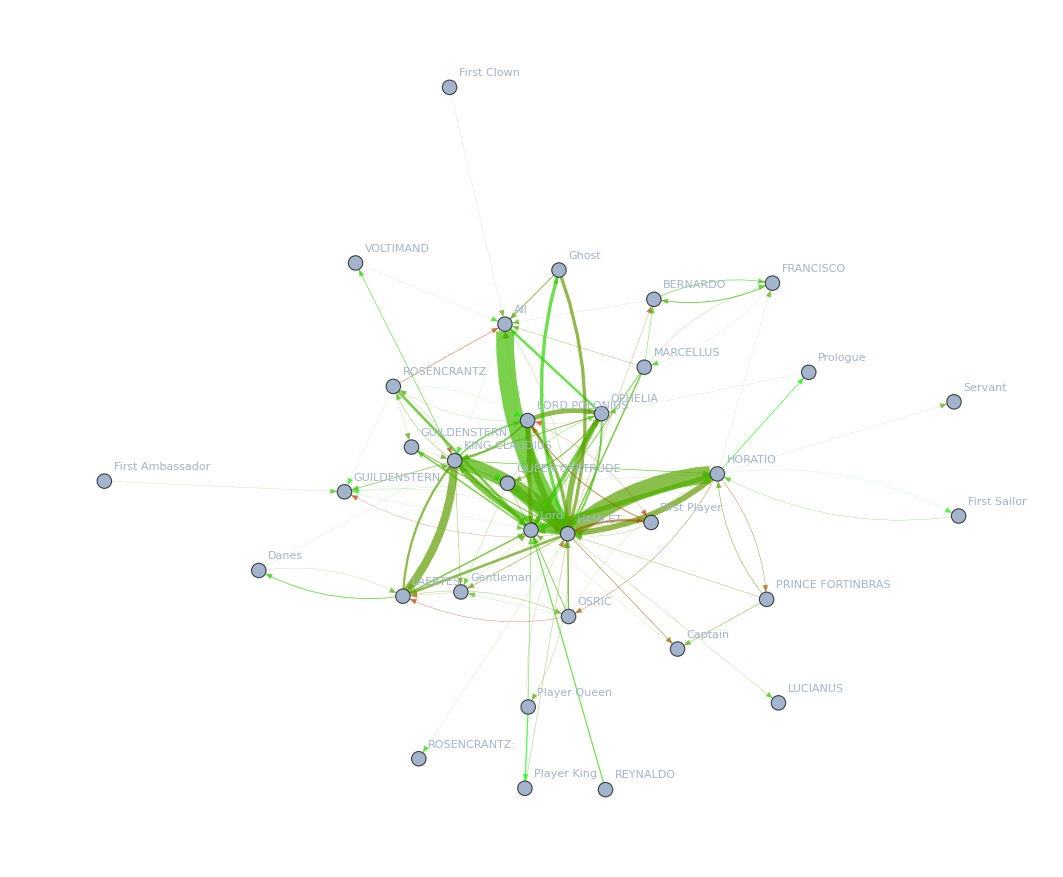

-Graphics-

```mathematica
edgeThickness=Thread[viableRules->(Thickness[#]&/@viableThickness)];
edgeFormat=Table[viableRules⟦i⟧->Directive[Values[edgeThickness]⟦i⟧,Values[edgeColors]⟦i⟧],{i,1,Length[edgeColors]}];
g=Graph[viableRules,VertexLabels->All,EdgeStyle->edgeFormat]
CommunityGraphPlot[g]
```